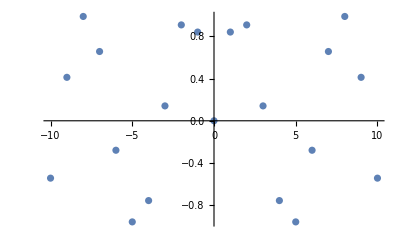

{{9.,0.412118},{6.,-0.279415}}

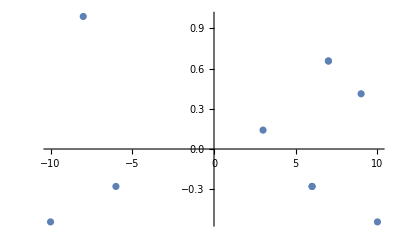

```mathematica
tab=Table[{i,Sin[Norm[{i}]]},{i,-10,10,1.}];
ListPlot[tab]
RandomChoice[tab,Floor[Length[tab]/10]]
ListPlot[RandomChoice[tab,Floor[Length[tab]/2]]]
```

```mathematica
tab=Flatten[Table[{i,j,Sin[Norm[{i,j}]]},{i,-10,10,1.},{j,-10,10,1.}],1];
ListPointPlot3D[tab]
RandomChoice[tab,Floor[Length[tab]/10]]
ListPointPlot3D[RandomChoice[tab,Floor[Length[tab]/10]]]
```

-Graphics3D-

{{-1.,4.,-0.831339},{3.,-6.,0.412338},{-8.,2.,0.924059},{-5.,0.,-0.958924},{10.,0.,-0.544021},{1.,9.,0.361049},{-6.,-5.,0.999044},{-5.,6.,0.999044},{6.,9.,-0.984036},{-2.,-1.,0.786749},{-2.,-4.,-0.971278},{-1.,5.,-0.926185},{3.,9.,-0.0620152},{0.,6.,-0.279415},{-9.,-10.,0.77534},{5.,6.,0.999044},{10.,-10.,0.999988},{-6.,3.,0.412338},{-10.,5.,-0.982979},{4.,-3.,-0.958924},{0.,6.,-0.279415},{-10.,-7.,-0.352101},{1.,-9.,0.361049},{-8.,-10.,0.237584},{6.,-8.,-0.544021},{-6.,-3.,0.412338},{10.,2.,-0.698473},{10.,2.,-0.698473},{5.,-6.,0.999044},{-1.,2.,0.786749},{5.,-10.,-0.982979},{-6.,8.,-0.544021},{4.,-7.,0.978389},{-7.,-3.,0.971762},{4.,6.,0.800373},{3.,-1.,-0.0206835},{6.,1.,-0.199084},{0.,-4.,-0.756802},{-9.,-2.,0.203796},{4.,9.,-0.411482},{5.,-5.,0.708861},{2.,-7.,0.839805},{4.,9.,-0.411482},{-1.,-6.,-0.199084}}

-Graphics3D-